# Gravitational Collapse Example Taken From Discussion of Mathematica Stack Exchange

Geoff Cope
University of Utah
February 1, 2021

## Hyperlink To Original Code and Discussion on Mathematica Stack Exchange

```mathematica
(* Just copied and ran code described here... haven't written or modified any of it *) 
Hyperlink["gravitational collapse in AdS",
"https://mathematica.stackexchange.com/questions/205035/can-ndsolve-address-spherical-gravitational-collapse"]
```

[gravitational collapse in AdS](https://mathematica.stackexchange.com/questions/205035/can-ndsolve-address-spherical-gravitational-collapse)

```mathematica
Hyperlink["On the nonlinear instability of confined geometries",
"https://arxiv.org/abs/1409.0533"]
```

[On the nonlinear instability of confined geometries](https://arxiv.org/abs/1409.0533)

## Hyperlink To Black Hole Workshops

```mathematica
Hyperlink["Black Hole Workshops",
"http://gravitation.web.ua.pt/node/163"]
```

[Black Hole Workshops](http://gravitation.web.ua.pt/node/163)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]


pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 1214 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,GeneralRelativityTensors`,VariationalMethods`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,System`,Global`}

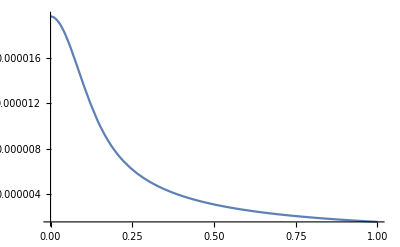
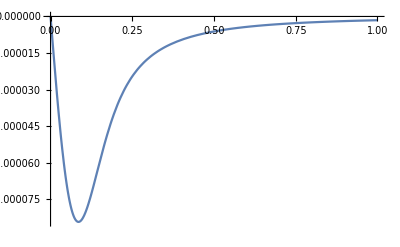

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

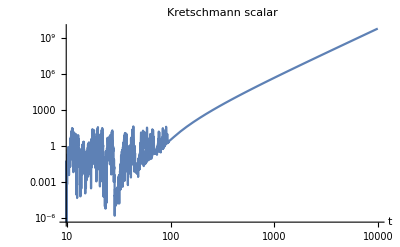

```mathematica
A=4/100;w=125/1000;
Pin[r_]:=A*Exp[-r^2/w^2]


PDE0=D[u[r],r,r]+2*D[u[r],r]/r==-Pi*Pin[r]^2*(1+u[r])^5;
(*eqs 23,24a*)

rmin=10^(-30);(*as close to r=0 as possible*)BC0={u'[rmin]==0,u'[1]==-u[1]};(*below eq 23*){initial,initial1}=NDSolveValue[{PDE0,BC0},{u,u'},{r,rmin,1},WorkingPrecision->30];


yin[r_]:=1+initial[r](*since ψ=1+u*)
ain[r_]:=1
Fin[r_]:=0
kin[r_]:=0

{Plot[initial[r],{r,rmin,1}],Plot[initial1[r],{r,rmin,1}]}


mu=0;{av1,av2,av3,av4,av5,av6,av7}={0,1,1,0,1,1,1} 10^-3;nn=3200;
rmin=1/nn;IC={k[0,r]==kin[r],F[0,r]==Fin[r],a[0,r]==ain[r],P[0,r]==Pin[r],y[0,r]==yin[r]};
BC1={F[t,1]==0,P[t,1]==0,k[t,1]==0,a[t,1]==1,y[t,1]==yin[1]};
BC2={Derivative[0,1][a][t,1]==0,Derivative[0,1][y][t,1]==0,Derivative[0,1][k][t,1]==0,Derivative[0,1][P][t,1]==0,Derivative[0,1][F][t,1]==0};BCreg={Derivative[0,1][F][t,rmin]==0,Derivative[0,1][a][t,rmin]==0,Derivative[0,1][k][t,rmin]==0};
eqy=D[y[t,r],t]==(-a[t,r]*y[t,r]*k[t,r]/6)+av1 D[y[t,r],r,r];

eqk=D[k[t,r],t]==(-(1/y[t,r]^4)*(D[a[t,r],r,r]+2*D[a[t,r],r]/r)-2*D[y[t,r],r]*D[a[t,r],r]/y[t,r]^5+(a[t,r]*k[t,r]^2)/3+4*Pi*a[t,r] (2 P[t,r]^2-mu^2 F[t,r]^2))+av2 D[k[t,r],r,r];

eqF=D[F[t,r],t]==(-a[t,r]*P[t,r])+av3 D[F[t,r],r,r];

eqP=D[P[t,r],t]==(a[t,r]*P[t,r]*k[t,r]-(a[t,r]/y[t,r]^4)*(D[F[t,r],r,r]+2*D[F[t,r],r]/r)-D[a[t,r],r]*D[F[t,r],r]/y[t,r]^4-2*a[t,r]*D[y[t,r],r]*D[F[t,r],r]/y[t,r]^5+mu^2 a[t,r] F[t,r])+av4 D[P[t,r],r,r];

eqa=D[a[t,r],t]==(-2*a[t,r]*k[t,r])+av5 D[a[t,r],r,r];
PDEs={eqy,eqk,eqF,eqP,eqa};
tmax=10000;
evolution=NDSolveValue[{PDEs,IC,BC1,BCreg},{y,k,F,P,a},{t,0,tmax},{r,rmin,1},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->nn,"MaxPoints"->nn,"DifferenceOrder"->4}},MaxSteps->10^6];
lb={y,k,F,P,a};

Table[Plot3D[evolution[[i]][t,r],{t,0,tmax},{r,rmin,1},Mesh->None,ColorFunction->"Rainbow",AxesLabel->Automatic,PlotLabel->lb[[i]],PlotRange->All],{i,1,5}]

(*Kretschmann scalar*)
ks=(2/27 (k[t,r]^4-24 Pi k[t,r]^2 (P[t,r]^2+mu^2 F[t,r]^2))+8 D[a[t,r],r,r]^2/(3 a[t,r]^2 y[t,r]^8)+8/3 (4 Pi^2 (11 P[t,r]^4-2 mu^2 P[t,r]^2 F[t,r]^2+5 mu^4 F[t,r]^4)))/.Flatten[Table[lb[[i]]->evolution[[i]],{i,1,5}]];

LogLogPlot[ks/.r->rmin,{t,0,tmax},PlotRange->All,PlotLabel->"Kretschmann scalar",AxesLabel->Automatic]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

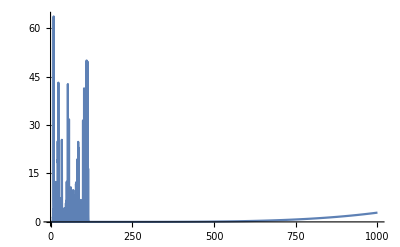

```mathematica
mu=4;{av1,av2,av3,av4,av5,av6,av7}={0,1,1,0,1,1,1} 10^-3;nn=999;
rmin=1/nn;IC={k[0,r]==kin[r],F[0,r]==Fin[r],a[0,r]==ain[r],P[0,r]==Pin[r],y[0,r]==yin[r],h[0,r]==0,m[0,r]==0};
BC1={F[t,1]==0,P[t,1]==0,k[t,1]==0,a[t,1]==1,y[t,1]==yin[1],h[t,1]==0,m[t,1]==0};
BCreg={Derivative[0,1][F][t,rmin]==0,Derivative[0,1][a][t,rmin]==0,Derivative[0,1][k][t,rmin]==0,h[t,rmin]==0,m[t,rmin]==0};
eqy=D[y[t,r],t]==(-a[t,r]*y[t,r]*k[t,r]/6)+av1 D[y[t,r],r,r];

eqk=D[k[t,r],t]==(-(1/y[t,r]^4)*(D[a[t,r],r,r]+2*D[a[t,r],r]/r)-2*D[y[t,r],r]*D[a[t,r],r]/y[t,r]^5+(a[t,r]*k[t,r]^2)/3+4*Pi*a[t,r] (2 P[t,r]^2-mu^2 F[t,r]^2))+av2 D[k[t,r],r,r];

eqF=D[F[t,r],t]==(-a[t,r]*P[t,r])+av3 D[F[t,r],r,r];

eqP=D[P[t,r],t]==(a[t,r]*P[t,r]*k[t,r]-(a[t,r]/y[t,r]^4)*(D[F[t,r],r,r]+2*D[F[t,r],r]/r)-D[a[t,r],r]*D[F[t,r],r]/y[t,r]^4-2*a[t,r]*D[y[t,r],r]*D[F[t,r],r]/y[t,r]^5+mu^2 a[t,r] F[t,r])+av4 D[P[t,r],r,r];

eqa=D[a[t,r],t]==(-2*a[t,r]*k[t,r])+av5 D[a[t,r],r,r];
eqh=D[h[t,r],t]==((D[y[t,r],r,r]+2/r D[y[t,r],r])/y[t,r]^5-k[t,r]^2/12+Pi (P[t,r]^2+D[F[t,r],r]^2/y[t,r]^4+mu^2 F[t,r]^2))+av6 D[h[t,r],r,r];
eqm=D[m[t,r],t]==(2/3 D[k[t,r],r]+8 Pi P[t,r] D[F[t,r],r])+av7 D[m[t,r],r,r];

PDEs={eqy,eqk,eqF,eqP,eqa,eqh,eqm};
tmax=1000;
evolution=NDSolveValue[{PDEs,IC,BC1,BCreg},{y,k,F,P,a,h,m},{t,0,tmax},{r,rmin,1},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->nn,"MaxPoints"->nn,"DifferenceOrder"->2}},MaxSteps->10^6];

lb={y,k,F,P,a,h,m};

Table[Plot3D[evolution[[i]][t,r],{t,0,tmax},{r,rmin,1},Mesh->None,ColorFunction->"Rainbow",AxesLabel->Automatic,PlotLabel->lb[[i]],PlotRange->All],{i,1,7}]
(*Kretschmann scalar*)
ks=(2/27 (k[t,r]^4-24 Pi k[t,r]^2 (P[t,r]^2+mu^2 F[t,r]^2))+8 D[a[t,r],r,r]^2/(3 a[t,r]^2 y[t,r]^8)+8/3 (4 Pi^2 (11 P[t,r]^4-2 mu^2 P[t,r]^2 F[t,r]^2+5 mu^4 F[t,r]^4)))/.Flatten[Table[lb[[i]]->evolution[[i]],{i,1,5}]];

Plot[ks/.r->rmin,{t,0,tmax},PlotRange->All]
```

```mathematica
A=4/100;w=125/1000;
Pin[r_]:=A*Exp[-r^2/w^2]


PDE0=D[u[r],r,r]+2*D[u[r],r]/r==-Pi*Pin[r]^2*(1+u[r])^5;
(*eqs 23,24a*)

rmin=10^(-30);(*as close to r=0 as possible*)BC0={u'[rmin]==0,u'[1]==-u[1]};(*below eq 23*){initial,initial1}=NDSolveValue[{PDE0,BC0},{u,u'},{r,rmin,1},WorkingPrecision->30];


yin[r_]:=1+initial[r](*since ψ=1+u*)
ain[r_]:=1
Fin[r_]:=0
kin[r_]:=0

{Plot[initial[r],{r,rmin,1}],Plot[initial1[r],{r,rmin,1}]}


mu=0;

rmin=10^-3;IC={k[0,r]==kin[r],F[0,r]==Fin[r],a[0,r]==ain[r],P[0,r]==Pin[r],y[0,r]==yin[r]};
BC1={F[t,1]==0,P[t,1]==0,k[t,1]==0,a[t,1]==1};
BC2={Derivative[0,1][a][t,1]==0,y[t,1]==yin[1]};BCreg={Derivative[0,1][F][t,rmin]==0,Derivative[0,1][a][t,rmin]==0};
eqy=D[y[t,r],t]==(-a[t,r]*y[t,r]*k[t,r]/6);

eqk=D[k[t,r],t]==(-(1/y[t,r]^4)*(D[a[t,r],r,r]+2*D[a[t,r],r]/r)-2*D[y[t,r],r]*D[a[t,r],r]/y[t,r]^5+(a[t,r]*k[t,r]^2)/3+4*Pi*a[t,r] (2 P[t,r]^2-mu^2 F[t,r]^2));

eqF=D[F[t,r],t]==(-a[t,r]*P[t,r]);

eqP=D[P[t,r],t]==(a[t,r]*P[t,r]*k[t,r]-(a[t,r]/y[t,r]^4)*(D[F[t,r],r,r]+2*D[F[t,r],r]/r)-D[a[t,r],r]*D[F[t,r],r]/y[t,r]^4-2*a[t,r]*D[y[t,r],r]*D[F[t,r],r]/y[t,r]^5+mu^2 a[t,r] F[t,r]);

eqa=D[a[t,r],t]==(-2*a[t,r]*k[t,r]);

PDEs={eqy,eqk,eqF,eqP,eqa};
tmax=3;
evolution=NDSolveValue[{PDEs,IC,BC1,BC2,BCreg},{y,k,F,P,a},{t,0,tmax},{r,rmin,1},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->40,"MaxPoints"->100,"DifferenceOrder"->"Pseudospectral"}},MaxSteps->10^6];
```

{-Graphics-,-Graphics-}